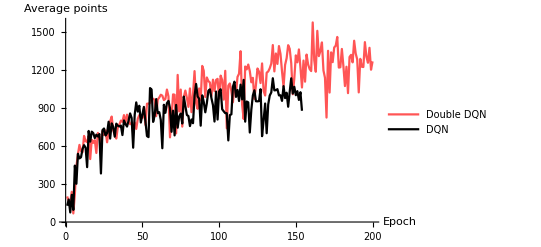

```mathematica
Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/space_invaders/results-doubleq.csv"];
rewardper=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/space_invaders/results-doubleq.csv"][[2;;,4]];
meanq=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/space_invaders/results-doubleq.csv"][[2;;,5]];
naturerewardper=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/space_invaders/results-20151201.csv"][[2;;-5,4]];
naturemeanq=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/space_invaders/results-20151201.csv"][[2;;-5,5]];
rewardperplot=ListPlot[{rewardper,naturerewardper},LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Average points"},PlotLegends->{"Double DQN","DQN"},PlotStyle->{Lighter[Red],Black}]
```

```mathematica
Export["/Users/cwalker32/Code/breakout_rl/report/dqn_si_rewardper.pdf",rewardperplot];
```

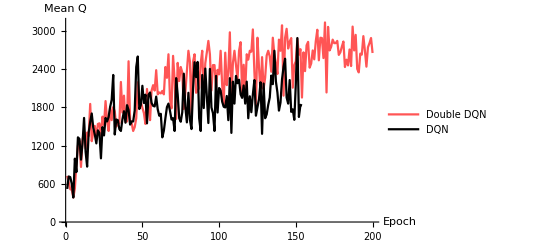

```mathematica
meanqplot=ListPlot[{meanq,naturemeanq},LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Mean Q"},PlotLegends->{"Double DQN","DQN"},PlotStyle->{Lighter[Red],Black}]
```

```mathematica
Export["/Users/cwalker32/Code/breakout_rl/report/dqn_si_meanq.pdf",meanqplot];
```